```mathematica
Table[Mod[2^r,21],{r,0,10}]
```

{1,2,4,8,16,11,1,2,4,8,16}

```mathematica
P[a_]:=Abs[Sum[Exp[2*Pi*I*(j*(3+a*2))/128],{j,0,7-1}]]^2//FullSimplify
```

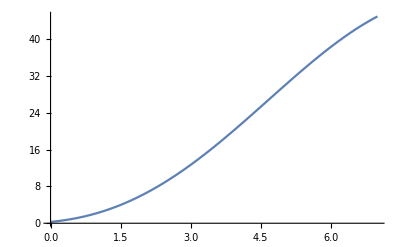

```mathematica
Plot[P[a],{a,0,7},PlotRange->All]
```

```mathematica
Abs[  Sum[Exp[2*Pi*I*j*(3*1-0)/Q],{j,0,p-1}]  ]^2//FullSimplify
```

Abs[(-1+ⅇ^((6 ⅈ p π)/Q))/(-1+ⅇ^((6 ⅈ π)/Q))]^2

```mathematica
P[p_]:=Abs[  Sum[Exp[2*Pi*I*j*(3*1-0)/16],{j,0,p-1}]  ]^2/p;
```

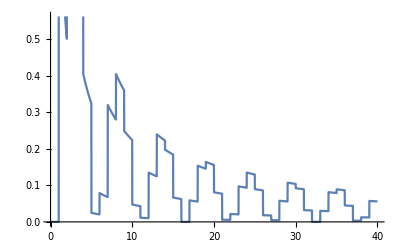

```mathematica
Plot[P[p],{p,0,40}]
```